# Demo

```mathematica
<<M2TeX`
```

## Options

Full definition

```mathematica
M2TeXOption["value","OpenCloseCharacter"->{"<Open>","<Close>"}];
%//M2TeXToString
```

<Open>value<Close>

Default for options also works with list of options

```mathematica
M2TeXOption["value"];
%//M2TeXToString
M2TeXOption[{"value",{"op2",{"op3","op4"}}}];
%//M2TeXToString
```

{value}

{value, op2, op3, op4}

Optional options

```mathematica
M2TeXOptionOptional[{"optional1","optional2"}];
%//M2TeXToString
```

[optional1, optional2]

## Commands

Full definition

```mathematica
M2TeXCommand[
"dostuff",
"Parameter"->"val1",
"ParameterOptional"->"val2",
"ParameterList"->None,
"StartCharacter"->"<\\>",
"EndCharacter"->"</>"
];
%//M2TeXToString
```

<\>dostuff[val2]{val1}</>

With parameter list, the type of options can be given by the user

```mathematica
M2TeXCommand[
"dostuff",
"ParameterList"->{
M2TeXOption[{"op1","op11"}],
M2TeXOptionOptional[{"op2","op22"}],
M2TeXOption["op3"]
}
];
%//M2TeXToString
```

\dostuff{op1, op11}[op2, op22]{op3}

Typical behavioud

```mathematica
M2TeXCommand["dostuff"];
%//M2TeXToString
M2TeXCommand["dostuff","opt"];
%//M2TeXToString
M2TeXCommand["dostuff",{"opt","OPT"},"opt2"];
%//M2TeXToString
M2TeXCommand["dostuff",,"opt2"];
%//M2TeXToString
```

\dostuff

\dostuff{opt}

\dostuff[opt2]{opt, OPT}

\dostuff[opt2]

Packages

```mathematica
M2TeXPackage["name",{"opt1","opt2"}];
%//M2TeXToString
```

\usepackage[opt1, opt2]{name}

## Environments

Full definition

```mathematica
M2TeXEnvironment[
"document",
"ParameterList"->{
M2TeXOption["op1"],
M2TeXOptionOptional["op2"]
},
"StartCommand"->"START",
"EndCommand"->"END"
];
%//M2TeXToString
```

START{op1}[op2]
END

Short definitions

```mathematica
M2TeXEnvironment["document"];
%//M2TeXToString
M2TeXEnvironment["document",{
M2TeXOption["op1"],
M2TeXOptionOptional["op2"]
}];
%//M2TeXToString
```

\begin{document}
\end{document}

\begin{document}{op1}[op2]
\end{document}

Add content to environment

```mathematica
doc=M2TeXEnvironment["document"];
M2TeXAddToEnvironment[doc,M2TeXCommand["section","Introduction"]]
M2TeXAddToEnvironment[doc,"Bla bla bla..."]
doc//M2TeXToString
```

\begin{document}
\section{Introduction}
Bla bla bla...
\end{document}

When an environment is added the next items are added inside that environment

```mathematica
doc=M2TeXEnvironment["document"];
M2TeXAddToEnvironment[doc,M2TeXEnvironment["picture"]]
M2TeXAddToEnvironment[doc,"Bla bla bla..."]
doc//M2TeXToString
```

\begin{document}
\begin{picture}
Bla bla bla...
\end{picture}
\end{document}

The M2TeXCloseActiveEnvironment command closes the active environment and returns to the previous one

```mathematica
doc=M2TeXEnvironment["document"];
M2TeXAddToEnvironment[doc,M2TeXEnvironment["picture"]]
M2TeXAddToEnvironment[doc,"picture"]
M2TeXCloseActiveEnvironment[doc]
M2TeXAddToEnvironment[doc,"Bla bla bla..."]
doc//M2TeXToString
```

\begin{document}
\begin{picture}
picture
\end{picture}
Bla bla bla...
\end{document}

The main environment can not be closed

```mathematica
doc=M2TeXEnvironment["document"];
M2TeXAddToEnvironment[doc,M2TeXEnvironment["picture"]]
M2TeXAddToEnvironment[doc,"Text1"]
M2TeXCloseActiveEnvironment[doc]
M2TeXAddToEnvironment[doc,"Text2"]
M2TeXCloseActiveEnvironment[doc]
M2TeXAddToEnvironment[doc,"Text3"]
doc//M2TeXToString
```

Error, depth not long enough!

\begin{document}
\begin{picture}
Text1
\end{picture}
Text2
Text3
\end{document}

The preamble is a list of items and is read/write

```mathematica
M2TeXToString/@doc[[1,"Preamble"]]
```

Missing[KeyAbsent,Preamble]

```mathematica
doc[[1,"Preamble"]]
```

Missing[KeyAbsent,Preamble]

Close all closes all child environments

```mathematica
doc=M2TeXEnvironment["document"];
M2TeXAddToEnvironment[doc,M2TeXEnvironment["picture"]]
M2TeXAddToEnvironment[doc,M2TeXEnvironment["pictureChild"]]
M2TeXCloseAll[doc]
M2TeXAddToEnvironment[doc,"content"]
doc//M2TeXToString
```

Sequence[1,Key[Content]]

\begin{document}
\begin{picture}
\begin{pictureChild}
\end{pictureChild}
\end{picture}
content
\end{document}

## Documents

Documents have the document environment and a document class and a preamble

```mathematica
doc=M2TeXDocument[
(* Command for document class *)
M2TeXCommand["documentclass","scrartcl","11pt"],
{
(* Optional: Preamble *)
M2TeXPackage["amsmath"],
M2TeXPackage["MinionPro","lf"]
}
];
doc//M2TeXToString
```

\documentclass[11pt]{scrartcl}

\usepackage{amsmath}
\usepackage[lf]{MinionPro}

\begin{document}
\end{document}

Documents behave the same way as environments

```mathematica
M2TeXAddToEnvironment[doc,"content"]
doc//M2TeXToString
```

\documentclass[11pt]{scrartcl}

\usepackage{amsmath}
\usepackage[lf]{MinionPro}

\begin{document}
content
\end{document}

Preamble is read/write

```mathematica
M2TeXToString/@doc[[1, "Preamble"]]
```

{\usepackage{amsmath},\usepackage[lf]{MinionPro}}

```mathematica
AppendTo[doc[[1, "Preamble"]],"% created with M2TeX"];
doc//M2TeXToString
```

\documentclass[11pt]{scrartcl}

\usepackage{amsmath}
\usepackage[lf]{MinionPro}
% created with M2TeX

\begin{document}
content
\end{document}

## Document templates

Following templates are available

```mathematica
M2TeXTemplates["article"];
%//M2TeXToString
```

\documentclass{scrartcl}

\usepackage[T1]{fontenc}
\usepackage[utf8]{inputenc}
\usepackage{amsmath}

\begin{document}
\end{document}

```mathematica
M2TeXTemplates["tikz"];
%//M2TeXToString
```

M2TeXTemplates[tikz]

## TikZ tools

Command for TikZ

```mathematica
M2TeXTikZCommand["node"];
%//M2TeXToString
M2TeXTikZCommand["node","at (0,0)"];
%//M2TeXToString
M2TeXTikZCommand["node","at (0,0)","black"];
%//M2TeXToString
M2TeXTikZCommand["node",,"black"];
%//M2TeXToString
```

\node;

\node at (0,0);

\node[black] at (0,0);

\node[black];

Axis for Pgf Plots

```mathematica
M2TeXTikZAxis["meins"];
%//M2TeXToString
```

\begin{axis}[meins]
\end{axis}

2D Plot from datapoints

```mathematica
M2TeXTikZPlot[{{1,3},{2,4}},{black,white}];
%//M2TeXToString
```

\addplot[black, white] coordinates{%
(1., 3.)%
(2., 4.)%
};

2D Plot from datapoints, with non numeric values

```mathematica
M2TeXTikZPlot[{{1,3},{a,4}},{black,white}];
%//M2TeXToString
```

Non numeric value!

\addplot[black, white] coordinates{%
(1., 3.)%
};

## Global document structure

A global document or environment can be set to simplify the commands

```mathematica
M2TeXSetGlobal[M2TeXEnvironment["doc"]]
M2TeXToStringGlobal[]
```

\begin{doc}
\end{doc}

Now the items are added to the global item if no parent item is given

```mathematica
M2TeXAddToEnvironment["text"]
M2TeXToStringGlobal[]
```

\begin{doc}
text
\end{doc}

If a string is given, a template will be set

```mathematica
M2TeXSetGlobal["article"]
M2TeXToStringGlobal[]
```

\documentclass{scrartcl}

\usepackage[T1]{fontenc}
\usepackage[utf8]{inputenc}
\usepackage{amsmath}

\begin{document}
\end{document}

## Compile LaTeX

Set the current directory, the pdf will be copied to this location

```mathematica
SetDirectory[NotebookDirectory[]];
```

Get plot points

```mathematica
TableFun[fun_]:=Table[
{x,fun[x]},
{x,0,3π,3π/500}
]
tableSin=TableFun[Sin];
tableCos=TableFun[Cos];
tableLog=TableFun[Log];
```

Plot options

```mathematica
width=5;
plotOptions={
"width="<>ToString[N[width],CForm]<>"cm",
"height="<>ToString[N[width/GoldenRatio],CForm]<>"cm",
"scale only axis"
}
```

{width=5.cm,height=3.090169943749474cm,scale only axis}

Generate an test example (add some preamble definitons to get multiple pages in standalone)

```mathematica
doc=M2TeXTemplates["standalone"];
AppendTo[doc[[1,"Preamble"]],M2TeXCommand["standaloneconfig","multi"]];
AppendTo[doc[[1,"Preamble"]],M2TeXCommand["newenvironment","ParameterList"->{
M2TeXOption["alone"],
M2TeXOption[M2TeXCommand["ignorespaces"]],
M2TeXOption[M2TeXCommand["ignorespacesafterend"]]
}]];
AppendTo[doc[[1,"Preamble"]],M2TeXCommand["standaloneenv","alone"]];
```

Create two pages with the same plot, one is clipped the other one not

```mathematica
M2TeXAddToEnvironment[doc,M2TeXEnvironment["alone"]];
M2TeXAddToEnvironment[doc,M2TeXTikZ[]];
M2TeXAddToEnvironment[doc,M2TeXTikZAxis[{plotOptions,"title=Full Plot"}]]
M2TeXAddToEnvironment[doc,M2TeXTikZPlot[tableSin,"blue, thick"]]
M2TeXAddToEnvironment[doc,M2TeXTikZPlot[tableCos,"red, thick"]]
M2TeXAddToEnvironment[doc,M2TeXTikZPlot[tableLog,"green, thick"]]
M2TeXCloseAll[doc];
```

```mathematica
M2TeXAddToEnvironment[doc,M2TeXEnvironment["alone"]];
M2TeXAddToEnvironment[doc,M2TeXTikZ[]];
M2TeXAddToEnvironment[doc,M2TeXTikZAxis[{plotOptions,"title=Clipped Plot,ymin=-2,xmax="<>ToString[N[2π]]}]]
M2TeXAddToEnvironment[doc,M2TeXTikZPlot[tableSin,"blue, thick"]]
M2TeXAddToEnvironment[doc,M2TeXTikZPlot[tableCos,"red, thick"]]
M2TeXAddToEnvironment[doc,M2TeXTikZPlot[tableLog,"green, thick"]]
```

Execute the example, the default output is a png copy of each page of the resulting pdf file
The option “SaveTeX” also copies the tex file in the working directory

```mathematica
M2TeXGeneratePDF["test",doc,"SaveTeX"->True]
```

Non numeric value!

Non numeric value!

{{-Graphics-,-Graphics-},{{},{},{}}}

This option “OutputPDF” imports the pdf file and not a png copy. Use with caution, there are some problems when importing pdfs into mathematica, see the non cliped plots

```mathematica
M2TeXGeneratePDF["test",doc,"OutputPDF"->True]
```

Non numeric value!

Non numeric value!

{{-Graphics-,-Graphics-},{{},{},{}}}

When an error / warning / overflow box occours the messages are output in the seccont list item

```mathematica
doc=M2TeXTemplates["article"];
M2TeXAddToEnvironment[doc,M2TeXCommand["lab\\el"]]
out=M2TeXGeneratePDF["test",doc][[2]]
```

LaTeX Error!

{{! Undefined control sequence.
l.8 \lab
        \el,!  ==> Fatal error occurred, no output PDF file produced!
Transcript written on M2TeX_0.log.},{},{}}

```mathematica
doc=M2TeXTemplates["article"];
M2TeXAddToEnvironment[doc,"text"]
M2TeXAddToEnvironment[doc,M2TeXCommand["label","newLabel"]]
M2TeXGeneratePDF["test",doc][[2]]
```

{{},{LaTeX Warning: Label(s) may have changed. Rerun to get cross-references right.},{}}

```mathematica
doc=M2TeXTemplates["article"];
M2TeXAddToEnvironment[doc,"abcdefg1234567890abcdefg1234567890abcdefg1234567890abcdefg1234567890abcdefg1234567890abcdefg1234567890"]
out=M2TeXGeneratePDF["test",doc][[2]]
```

{{},{},{Overfull \hbox (137.03363pt too wide) in paragraph at lines 8--9}}

Compile global document

```mathematica
M2TeXSetGlobal["standalone"]
M2TeXAddToEnvironment["Text"]
M2TeXGeneratePDF["test"]
```

{{-Graphics-},{{},{},{}}}

# Other useful stuff

Get lines from plot, usually there is a reasonable amount of datapoints

{234,214,368,2,2}

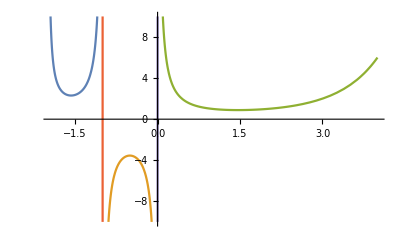

```mathematica
plt=Plot[Gamma[x],{x,-2,4},PlotRange->{-10,10}];
lines=Select[Flatten[plt[[1]]],Head@#==Line&][[All,1]];
Length/@lines
ListLinePlot[lines]
```

{433,574,996,1306,1601}

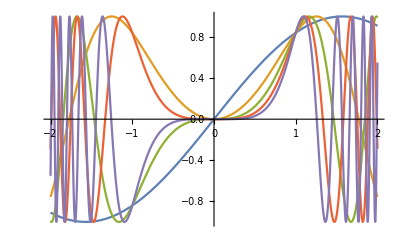

```mathematica
plt=Plot[Table[Sin[x^i],{i,5}],{x,-2,2}];
lines=Select[Flatten[plt[[1]]],Head@#==Line&][[All,1]];
Length/@lines
ListLinePlot[lines]
```